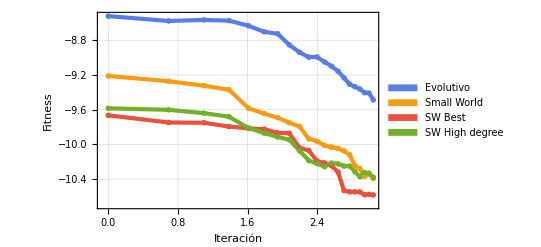

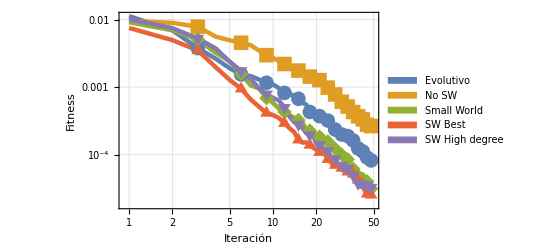

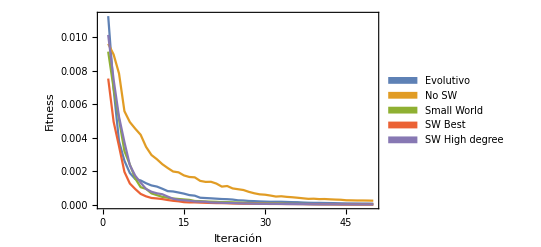

```mathematica
evolutivo = {0.011237026,0.006907525,0.003784185,0.002628957,0.001898943,0.001540456,0.001456965,0.001291133,0.001160045,0.001092892,0.000965121,0.000822429,0.000802012,0.000739274,0.000673027,0.000585469,0.000551818,0.00042896,0.000411117,0.000393598,0.000372615,0.000351586,0.000342284,0.000320528,0.000274182,0.00026484,0.00023597,0.000226975,0.000210087,0.000198978,0.000188174,0.000190433,0.000188923,0.000178206,0.000166013,0.00016238,0.000142844,0.000131147,0.000123988,0.000124287,0.000117414,0.000111737,0.000105498,0.000097761,0.000090757,0.000088251,0.000085883,0.000082378,0.000082018,0.000075801};
nosw = {0.009591637,0.008953498,0.007823382,0.005579703,0.004930339,0.004536574,0.004174886,0.003455074,0.002970095,0.002720121,0.002426292,0.002197741,0.001988597,0.001940197,0.001756434,0.001663846,0.001641848,0.0014322,0.001371615,0.001377836,0.00127107,0.001091389,0.001126283,0.000982768,0.000935504,0.000888136,0.000778783,0.000694185,0.000630649,0.000609154,0.000558115,0.000498886,0.000516262,0.000480433,0.000458281,0.000428066,0.000394582,0.000361861,0.000371226,0.000346631,0.000351799,0.000333804,0.000318816,0.000308283,0.000277231,0.000272991,0.000264482,0.000265066,0.000260333,0.000252461};
sw={0.009123976,0.006939739,0.005086746,0.003205094,0.002407272,0.001574977,0.001056309,0.000955642,0.000688245,0.000584276,0.000480344,0.000429738,0.000383497,0.000354077,0.000326389,0.000302188,0.00023496,0.000227121,0.000205146,0.000194857,0.000185184,0.000166519,0.000166219,0.000156901,0.00014049,0.000130719,0.000122306,0.000103083,0.000103005,0.000099841,0.00009401,0.000089273,0.000085287,0.000068952,0.0000647,0.000061831,0.000058227,0.000055811,0.00004846,0.00004705,0.000044866,0.000043978,0.000043354,0.000042114,0.00004027,0.000035512,0.000034307,0.000031392,0.000032633,0.000030653};
swbest = {0.007520310,0.004956273,0.003492597,0.001968500,0.001275896,0.000945908,0.000655285,0.000510403,0.000414636,0.000386257,0.000348435,0.000292815,0.000246793,0.000216539,0.000166107,0.000150972,0.000152603,0.000139023,0.000127313,0.000118132,0.000108812,0.000107758,0.000100310,0.000085668,0.000078554,0.000071670,0.000070056,0.000070225,0.000066646,0.000063450,0.000058456,0.000058278,0.000055769,0.000054633,0.000054103,0.000051858,0.000051604,0.000043643,0.000042376,0.000037510,0.000036664,0.000035444,0.000033045,0.000026690,0.000026281,0.000026281,0.000026254,0.000025418,0.000025547,0.000025350};
swhd ={0.010117900,0.007458299,0.005243691,0.003735475,0.002369509,0.001739582,0.001324713,0.000951148,0.000785356,0.000691800,0.000636235,0.000496734,0.000367552,0.000304324,0.000279566,0.000249806,0.000208208,0.000195313,0.000192921,0.000143600,0.000140128,0.000128985,0.000118991,0.000114090,0.000096098,0.000089829,0.000086934,0.000075802,0.000072098,0.000068798,0.000067616,0.000065057,0.000062479,0.000054869,0.000051726,0.000049481,0.000047908,0.000042233,0.000037717,0.000036394,0.000035127,0.000036615,0.000036286,0.000035362,0.000035386,0.000033128,0.000031283,0.000032784,0.000032379,0.000031124};

ListLogLogPlot[{evolutivo[[30;;50]],sw[[30;;50]],swbest[[30;;50]],swhd[[30;;50]]},Joined->True,PlotRange->Full, GridLines->Automatic, FrameTicksStyle->Directive[Black,15],Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","Small World","SW Best","SW High degree"}], PlotTheme->"Business"]

ListLogLogPlot[{evolutivo,nosw,sw,swbest,swhd},Joined->True,PlotRange->Full,GridLines->Automatic, FrameTicksStyle->Directive[Black,15], Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","No SW","Small World","SW Best","SW High degree"}],Mesh->{Range[0,50,3]},PlotMarkers->{Automatic,15},PlotStyle->{Thickness[0.008]}]
```